32. (p.250) Show the difference patterns by altering the evolution of  CellularAutomaton[30,IntegerDigits[#,2,n],11]

```mathematica
ArrayPlot[CellularAutomaton[30,IntegerDigits[12345,2,101],50]]
```

-Graphics-

at a single random position during the evolution.  Collect a sample of these patterns.  Make an ArrayPlot where the cell is 0 for originally 0, 1 for originally 1, 2 for an altered original 0, 3 for an altered original 1.

```mathematica
OriginalCA=CellularAutomaton[30,IntegerDigits[12345,2,101],50];
```

```mathematica
RandomPosition:={RandomInteger[{1,50}],RandomInteger[{1,100}]}
```

```mathematica
RandomX:= RandomInteger[{1,51}];
```

```mathematica
RandomY:= RandomInteger[{1,101}];
```

```mathematica
AlteredCA[position_]:= With[{step=Flatten[CellularAutomaton[30,IntegerDigits[12345,2,101],position[[1]],-1]]},Join[CellularAutomaton[30,IntegerDigits[12345,2,101],position[[1]]-1],CellularAutomaton[30,If[step[[position[[2]]]]==1,ReplacePart[step,position[[2]]->0],ReplacePart[step,position[[2]]->1]],50-position[[1]]]]]
```

```mathematica
(*OR*)
```

```mathematica
AlteredCA2[x_, y_] := With[{evolution = CellularAutomaton[30,IntegerDigits[12345,2,101], 50]},
	Replace[evolution + 2 Join[evolution[[;;x - 1]], CellularAutomaton[30, MapAt[Mod[# + 1, 2]&, evolution[[x]], {y}], 50 - x + 1]],
	{3-> 1, 1 -> 3}, {2}]
]
```

```mathematica
(* oldCA+2newCA = {0,1,2,3} since: *)
```

```mathematica
#1.{x,y} +c== #2&@@@{{{0,0} ,0},
{{1,1} ,1},
{{0,1} , 2},
{{1, 0} ,3}}
```

{c==0,c+x+y==1,c+y==2,c+x==3}

```mathematica
#1.{1,2}&@@@{{{0,0} ,0},
{{1,1} ,1},
{{0,1} , 2},
{{1, 0} ,3}}
```

{0,3,2,1}

```mathematica
Dimensions[AlteredCA[RandomPosition]]
```

{51,101}

```mathematica
Dimensions[AlteredCA2[RandomX,RandomY]]
```

{51,101}

```mathematica
{ArrayPlot[AlteredCA[RandomPosition]],ArrayPlot[OriginalCA]}
```

{-Graphics-,-Graphics-}

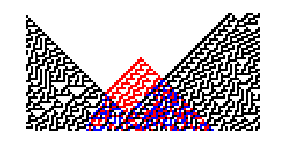

```mathematica
ArrayPlot[AlteredCA2[20,50], ColorRules ->{0 -> White, 1 -> Black, 2 -> Red, 3 -> Blue}]
```

```mathematica
ShowChanges[originalCA_,alteredCA_]:= ArrayPlot[ReplacePart[ReplacePart[alteredCA,#->2]& @ Position[originalCA-alteredCA,-1,2],#->3]& @ Position[originalCA-alteredCA,1,2]]
```

```mathematica
ShowChanges2[alteredCA_]:= ArrayPlot[alteredCA,ColorRules->{0 -> White, 1 -> Black, 2 -> Red, 3 -> Blue}]
```

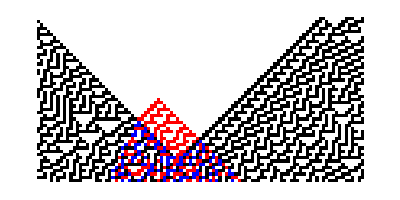
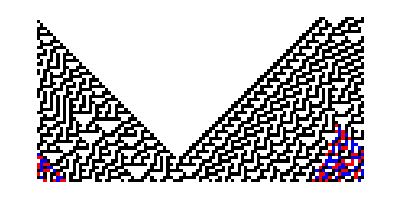
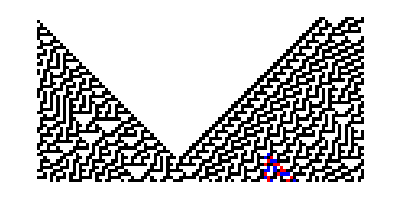
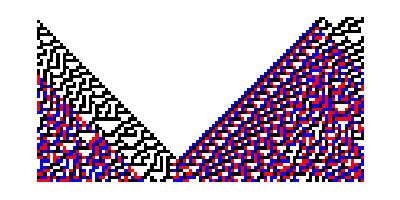
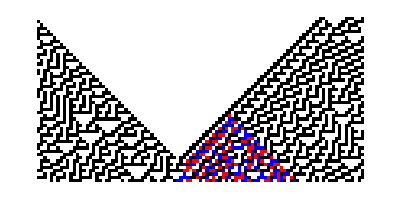
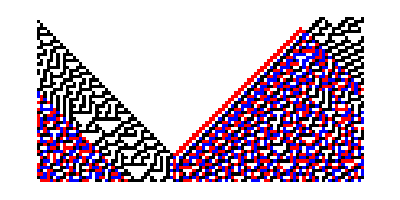
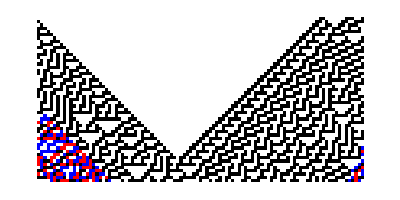
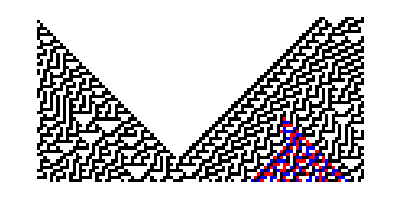

```mathematica
Table[ShowChanges2[AlteredCA2[RandomX,RandomY]],{i,10}]
```

```mathematica
Table[ShowChanges[OriginalCA,AlteredCA[RandomPosition]],{i,10}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}